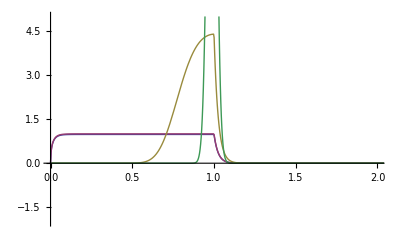

```mathematica
(* Here we simulate how many collisions are necessary to slow down a neutron on average *)
(* MassA: Mass number *)
alph[MassA_]:=N[((MassA-1)/(MassA+1))^2];
(* Ef: energy after collision; Ei: original energy *)
(* simple scattering off an infinitely heavy nucleus at rest *)
Ef[Ei_,a_]:=RandomReal[{a*Ei,Ei}];
(* scattering kernel for a proton gas at temperature T *)
(* free atom scattering cross section for hydrogen *)
k=(8.6173324*10^-5); (* eV/K *)
T=293; (* K *)
sigmaHfree=1;
(* Duderstadt page 53 *)
ProtonKernel[Ei_,Ef_]:=(sigmaHfree/Ei)*If[Ei≥ Ef,Erf[Sqrt[Ef/(k*T)]],Exp[(Ei-Ef)/(k*T)]*Erf[Sqrt[Ei/(k*T)]]];

sigmaNfree=1;
thet[MassA_]:=(MassA+1)/(2*Sqrt[MassA]);
ro[MassA_]:=(MassA-1)/(2*Sqrt[MassA]);

f[Ei_,Ef_,MassA_]:=sigmaNfree*(thet[MassA])^2/(2*Ei)*1*((Erf[thet[MassA]*Sqrt[Ei/(k*T)]-ro[MassA]*Sqrt[Ef/(k*T)]]-Erf[thet[MassA]*Sqrt[Ei/(k*T)]+ro[MassA]*Sqrt[Ef/(k*T)]])+(Erf[thet[MassA]*Sqrt[Ef/(k*T)]-ro[MassA]*Sqrt[Ei/(k*T)]]+Erf[thet[MassA]*Sqrt[Ef/(k*T)]+ro[MassA]*Sqrt[Ei/(k*T)]]));

(* Duderstadt page 388 *)
NuklideKernel[Ei_,Ef_,MassA_]:=If[Ei<Ef,sigmaNfree*(thet[MassA])^2/(2*Ei)*Exp[-(Ef-Ei)/(k*T)]*((Erf[thet[MassA]*Sqrt[Ei/(k*T)]-ro[MassA]*Sqrt[Ef/(k*T)]]+Erf[thet[MassA]*Sqrt[Ei/(k*T)]+ro[MassA]*Sqrt[Ef/(k*T)]])+(Erf[thet[MassA]*Sqrt[Ef/(k*T)]-ro[MassA]*Sqrt[Ei/(k*T)]]-Erf[thet[MassA]*Sqrt[Ef/(k*T)]+ro[MassA]*Sqrt[Ei/(k*T)]])),f[Ei,Ef,MassA]];

Plot[{0.98*ProtonKernel[1,x],NuklideKernel[1,x,1],NuklideKernel[1,x,16],NuklideKernel[1,x,235]},{x,0,10},PlotRange->{{0,2},{-2,5}}]
```

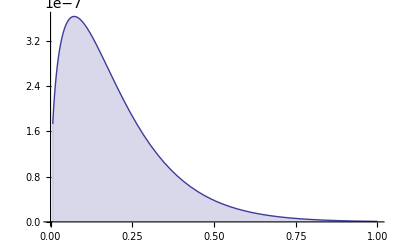

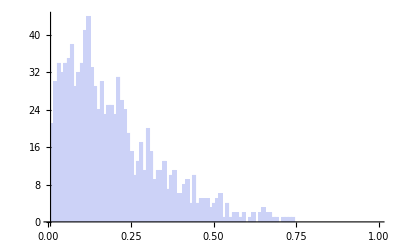

```mathematica
(* prompt U235 fission spectrum *)
Nrm=986229; (* normalized to 1 between 0.5 and 10 MeV *)
s235U[en_]:=0.453*Exp[-1.036*en/10^6]*Sinh[Sqrt[2.29*en/10^6]]/Nrm;
s235UP=ProbabilityDistribution[s235U[x],{x,64700,10*10^6}];
dis=RandomVariate[s235UP,1000];

Plot[Evaluate[PDF[s235UP,x]], {x,0,10*10^6},Filling->Axis]
Histogram[dis,{64700,10*10^6,100000}]
```

{1000,999}

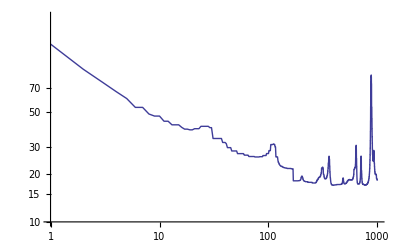

```mathematica
MyProb=ProbabilityDistribution[NuklideKernel[100,x,235],{x,1,10000}];
SlowMeDownNext=1.0;

(* NGet235 is an approximaion to the computationally expensive solution of: NSolve[(f[Estart,Eff,kern]==0.1*f[Estart,Estart,kern]) && (0.01*Estart<Eff<Estart),Eff,Reals,WorkingPrecision->1] *)

NGet235[Es_,ke_]:=Module[{j,soli},
For[j=1,j<100,soli=f[Es,Es*(1-j*0.01),ke];
If[soli<0.01*f[Es,Es,ke],Break[]];
j++];
Es*(1-j*0.01)
];

SlowMeDown[Estart_,kern_]:=Module[{tup,sol,xk,Eff},
If[kern==1,
MyProb=ProbabilityDistribution[NuklideKernel[Estart,x,kern],{x,Max[0.0025,Estart/1000],If[Estart>64700,Estart,5*Estart]}]; 
SlowMeDownNext=RandomVariate[MyProb]; 

Clear[sol,xk,Eff,MyProb];
];

If[kern>200,
(*
sol=NSolve[(f[Estart,Eff,kern]==0.01*f[Estart,Estart,kern]) && (0.0<Eff<Estart),Eff,Reals][[1]][[1]];
xk=Eff/.sol;
*)
xk=NGet235[Estart,kern];
MyProb=ProbabilityDistribution[NuklideKernel[Estart,x,kern] ,{x,Max[0.0025,xk],If[Estart>64700,Estart,1.1*Estart]}] ;
SlowMeDownNext=RandomVariate[MyProb]; 
(*SlowMeDownNext=RandomVariate[ProbabilityDistribution[NuklideKernel[Estart,x,kern] ,{x,Max[0.0025,xk],If[Estart>64700,Estart,1.1*Estart]}]];*)
Clear[sol,xk,Eff,MyProb];
];
];
(* we have to catch Mathematica underflow issues here, therefore above 64keV only downscattering *)

(* SetDirectory["C:\\MathematicWork\\endf\\"]; *)
SetDirectory["C:\\Users\\Documents\\n-ENDF-VII0.endf\\endf-sigmaPlot\\"];
H1Elastic=Import["H-1-elastic.txt","csv"];
U235Total=Import["U-235-total.txt","csv"];
U235Elastic=Import["U-235-elastic.txt","csv"];
U235Gamma=Import["U-235-gamma.txt","csv"];
U235Fission=Import["U-235-fission.txt","csv"];

nh1e=Length[H1Elastic];
nu235t=Length[U235Total];
nu235e=Length[U235Elastic];
nu235g=Length[U235Gamma];
nu235f=Length[U235Fission];

CleanUp[data_]:=Module[{i=Length[data],j,x1,x2,y2,lis},
lis=data;
For[j=2,j<i,
x1=lis[[j]][[1]];
x2=lis[[j+1]][[1]];
y2=lis[[j+1]][[2]];
If[x1==x2,lis=ReplacePart[lis,(j+1)->{x2+0.0001,y2}];];
j++;];
lis
];

U235Totalc=CleanUp[U235Total];
U235Elasticc=CleanUp[U235Elastic];
U235Gammac=CleanUp[U235Gamma];
U235Fissionc=CleanUp[U235Fission];

ih1e=Interpolation[H1Elastic[[2;;nh1e]],InterpolationOrder->0];
iu235t=Interpolation[U235Totalc[[2;;nu235t]],InterpolationOrder->0];
iu235e=Interpolation[U235Elasticc[[2;;nu235e]],InterpolationOrder->0];
iu235g=Interpolation[U235Gammac[[2;;nu235g]],InterpolationOrder->0];
iu235f=Interpolation[U235Fissionc[[2;;nu235f]],InterpolationOrder->0];

nH=1;nU=0.1;

MYbinstore=HistogramList[{0},{0.01,10,0.01}][[2]];
MYbins=HistogramList[{0},{0.01,10,0.01}][[1]];

Print[{Length[MYbins],Length[MYbinstore]}];


SH[x_]:=nH*ih1e[x]; SU[x_]:=nU*iu235f[x];
xss={};
For[k=1,k≤Length[MYbins],AppendTo[xss,SH[MYbins[[k]]]+SU[MYbins[[k]]]];k++];
ListLogLogPlot[xss,PlotRange->{{1,1000},{10,200}},Joined->True]
```

```mathematica
EventList[runs_]:=Module[{Estart,Enext,tuppel,ti,slows,SigmaH,SigmaU,rs,r1,r2,r3,hit,x1,x2},
Estart=RandomVariate[s235UP];tuppel={Estart};

Do[
(* Print[Estart]; *)
(* determine total interaction frequencies *)
SigmaH=nH*ih1e[Estart]; SigmaU=nU*iu235t[Estart];
rs=RandomReal[];
(* interaction with hydrogen *)
If[rs≤SigmaH/(SigmaH+SigmaU),rs=1,rs=2];
(* interaction with uranium *)
If[rs==1,SlowMeDown[Estart,1];Enext=SlowMeDownNext;];
If[rs==2,rs=RandomReal[];r1=iu235e[Estart];r2=iu235g[Estart];r3=iu235f[Estart];
If[rs≤r1/(r1+r2+r3),(*Print[{"235 :",Estart}];*)SlowMeDown[Estart,235];Enext=SlowMeDownNext;];
If[rs≤r2/(r1+r2+r3) && rs>r1/(r1+r2+r3) ,Enext=0;];
If[rs≥r3/(r1+r2+r3)   ,Enext=0;];
];

(* Print[{Estart,Enext,rs}]; *)
Estart=N[Enext,4];
If[Estart>0,AppendTo[tuppel,Enext],ti=Drop[tuppel,-1];Clear[tuppel];tuppel=ti;];
Clear[rs,r1,r2,r3,SigmaH,SigmaU,Enext];
If[Estart≤ 0.0025,Break[]],
{runs}];

(* MYbinstore=HistogramList[tuppel,{0,10000,1}][[2]];*)
Print[{Length[tuppel],tuppel}]; 
For[r1=1,r1≤Length[MYbins]-1,
x1=MYbins[[r1]];x2=MYbins[[r1+1]];
For[r2=1,r2≤Length[tuppel],
If[tuppel[[r2]]≥x1 && tuppel[[r2]]<x2,MYbinstore[[r1]]=MYbinstore[[r1]]+1;Break[];];
r2++];
Clear[x1,x2];
r1++];

Clear[Estart,tuppel];
];

$HistoryLength=0;
Off[General::unfl];
Off[CompiledFunction::cfexe];
Off[Refine::fas];
Off[CompiledFunction::cfse];
N[NuklideKernel[10^6,1.99999999*10^1,235],3]
(*
SlowMeDown[0.003,235];Print[SlowMeDownNext]; 
SlowMeDown[2.0*10^6,235];Print[SlowMeDownNext]; 
*)
{iu235g[0.5],iu235f[0.5],iu235e[0.5],nH*ih1e[0.5],nU*iu235t[0.5]}
```

0.

{9.45794,78.3446,13.0291,20.2988,9.76164}

```mathematica
For[h=1,h<100000,EventList[1000];ClearSystemCache[];If[FractionalPart[(h/1)]==0,Print[{h,Total[MYbinstore]}];];h++] ;
```

{8,{2.73921×10^6,1.19683×10^6,791161.,544118.,261710.,174538.,206533.,135854.}}

{1,0}

{0,{}}

{2,0}

{1,{1.68104×10^6}}

{3,0}

{8,{1.71032×10^6,1.23926×10^6,926121.,754196.,218315.,60510.8,30759.9,54849.9}}

{4,0}

{21,{1.22563×10^6,654312.,565810.,438695.,320290.,236856.,211121.,110853.,183846.,246377.,204975.,167046.,248876.,87111.4,104097.,132036.,228573.,146492.,213288.,128590.,208066.}}

{5,0}

{1,{583305.}}

{6,0}

{1,{7.18932×10^6}}

{7,0}

{3,{713684.,476581.,466780.}}

{8,0}

{1,{388837.}}

{9,0}

{28,{1.06423×10^6,574704.,537961.,461541.,53695.,110056.,198993.,285945.,314541.,77678.,13979.7,26978.3,50821.9,126176.,114103.,11942.6,46982.6,102881.,158234.,175885.,177917.,54839.4,121818.,192262.,61378.2,48327.8,101054.,135225.}}

{10,0}

{1,{2.94838×10^6}}

{11,0}

{0,{}}

{12,0}

{1,{3.21436×10^6}}

{13,0}

{26,{3.31953×10^6,466655.,155344.,158668.,79392.1,156734.,139197.,179767.,138131.,21516.2,50054.7,115882.,198783.,201417.,307791.,239870.,84483.8,111828.,140727.,92077.6,75541.3,66030.4,102941.,129677.,191964.,177042.}}

{14,0}

{2,{635425.,614713.}}

{15,0}

{0,{}}

{16,0}

{11,{918368.,65242.1,88066.4,89106.2,110933.,103488.,89046.5,54731.1,86469.9,103228.,49605.4}}

{17,0}

{24,{2.2917×10^6,1.52975×10^6,1.02624×10^6,350907.,395370.,454875.,554896.,508899.,557937.,688537.,88436.4,89640.6,148663.,231705.,162652.,24117.6,68133.7,6507.09,13169.8,3784.52,25051.6,83078.7,121507.,28834.8}}

{18,0}

{6,{2.70143×10^6,2.053×10^6,712586.,691065.,511925.,236752.}}

{19,0}

{8,{1.35506×10^6,995112.,448629.,363184.,266638.,241369.,62253.7,48504.3}}

{20,0}

{25,{2.73127×10^6,1.92437×10^6,1.97002×10^6,1.43923×10^6,305970.,73453.5,107047.,56629.1,156132.,202443.,139376.,63390.7,103928.,184289.,239822.,235255.,169790.,211704.,317360.,101145.,183994.,89655.4,165726.,5399.87,19823.6}}

{21,0}

{26,{1.04837×10^6,1.17978×10^6,1.2811×10^6,151210.,161462.,187320.,181950.,120297.,50301.6,65984.4,121584.,159645.,220146.,226931.,217022.,10372.9,18077.5,64619.9,26170.4,80546.,109100.,190210.,187035.,251857.,319935.,259167.}}

{22,0}

{4,{2.12917×10^6,1.84352×10^6,1.44631×10^6,302921.}}

{23,0}

$Aborted

```mathematica
Total[MYbinstore]
```

14609

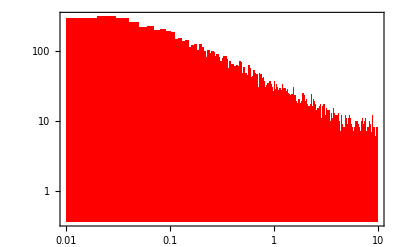

```mathematica
data={0};
Histogram[data,{MYbins},MYbinstore &,Axes->True,Ticks->Automatic,FrameTicks->Automatic,Frame->True,ScalingFunctions->{"Log","Log"},ChartStyle->{Red}]
```

```mathematica
Export["SlowMeDown05-13aData001.dat",{MYbins,MYbinstore},"Table"]
```

SlowMeDown05-13aData001.dat